```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.4,Jtwo,0.4,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.36514837167011066}]
```

{z→0.365148}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.4,l->0.4}
```

0.365148+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=Check[FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
],{z->0}];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.36514837167011066]]
```

{{0.005,0.37608},{0.01,0.386581},{0.015,0.396679},{0.02,0.406394},{0.025,0.415747},{0.03,0.424751},{0.035,0.433421},{0.04,0.441766},{0.045,0.449796},{0.05,0.457516},{0.055,0.464931},{0.06,0.472046},{0.065,0.478862},{0.07,0.485381},{0.075,0.491603},{0.08,0.497527},{0.085,0.503153},{0.09,0.508476},{0.095,0.513496},{0.1,0.518209}}

```mathematica
moduler[Lister[-1,-0.005,0.36514837167011066]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.47886}. NIntegrate obtained 21.9611 and 21.5951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.06776}. NIntegrate obtained 0.190094 and 0.197737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.58916}. NIntegrate obtained 0.11243 and 0.152342 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{-0.005,0.353754},{-0.01,0.341858},{-0.015,0.329415},{-0.02,0.316365},{-0.025,0.302639},{-0.03,0.288147},{-0.035,0.272773},{-0.04,0.256365},{-0.045,0.238718},{-0.05,0.219539},{-0.055,0.198392},{-0.06,0.174571},{-0.065,0.146788},{-0.07,0.112146},{-0.075,0.0597273},{-0.08,0},{-0.085,0},{-0.09,0},{-0.095,0},{-0.1,0}}

```mathematica
P = ListPlot[{{0.005,0.3760802101956303},{0.01,0.3865814323597306},{0.015,0.39667869196216266},{0.02,0.4063942385972723},{0.025,0.41574663984085763},{0.03,0.4247513438698238},{0.035,0.4334211237913019},{0.04,0.44176643330567483},{0.045,0.44979569541162406},{0.05,0.45751554038816944},{0.055,0.464931005443647},{0.06,0.47204570567482623},{0.065,0.4788619839856866},{0.07,0.48538104612627503},{0.075,0.4916030858705241},{0.08,0.49752740442781246},{0.085,0.5031525273915853},{0.09,0.5084763218015912},{0.095,0.5134961151864673},{0.1,0.5182088177292198},{-0.005,0.3537539182557586},{-0.01,0.3418582622203128},{-0.015,0.3294145502870945},{-0.02,0.3163653589410917},{-0.025,0.30263944982321717},{-0.03,0.2881470728553941},{-0.035,0.27277293774126105},{-0.04,0.2563652657506737},{-0.045,0.23871787043422685},{-0.05,0.21953893356367007},{-0.055,0.1983919539313645},{-0.06,0.17457079356808466},{-0.065,0.1467876817436544},{-0.07,0.11214583653343176},{-0.075,0.05972725862177993},{-0.08,0},{-0.085,0},{-0.09,0},{-0.095,0},{-0.1,0}}]
```

```mathematica
FindRoot[NullsHolm[-0.08,z],{z,0.05972725862177993}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.47886}. NIntegrate obtained 21.9611 and 21.5951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.06776}. NIntegrate obtained 0.190094 and 0.197737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.58916}. NIntegrate obtained 0.11243 and 0.152342 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{z→-0.240122}

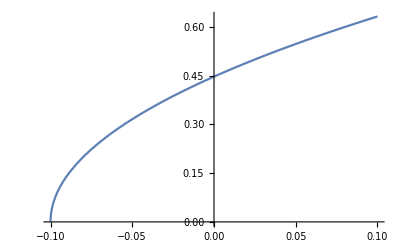

```mathematica
G = Plot[Sqrt[1+2*(0.4*Cos[Inv[0.4,Jtwo]]+Jtwo*Cos[2*Inv[0.4,Jtwo]])],{Jtwo,-0.1,0.1}]
```

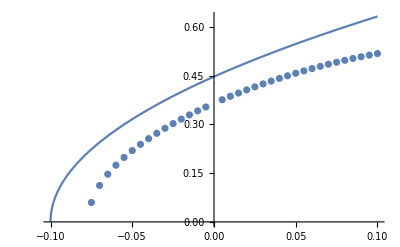

```mathematica
Show[G,P]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
differ[-1,0.4,moduler[Lister[-1,-0.005,0.36514837167011066]]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.47886}. NIntegrate obtained 21.9611 and 21.5951 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.06776}. NIntegrate obtained 0.190094 and 0.197737 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.58916}. NIntegrate obtained 0.11243 and 0.152342 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{-0.005,0.082136},{-0.01,0.0824058},{-0.015,0.082896},{-0.02,0.0836346},{-0.025,0.0846589},{-0.03,0.0860187},{-0.035,0.0877822},{-0.04,0.0900449},{-0.045,0.0929446},{-0.05,0.0966888},{-0.055,0.101608},{-0.06,0.108272},{-0.065,0.117787},{-0.07,0.132803},{-0.075,0.16388},{-0.08,0.2},{-0.085,0.173205},{-0.09,0.141421},{-0.095,0.1},{-0.1,0.}}

```mathematica
differ[1,0.4,moduler[Lister[1,0.005,0.36514837167011066]]]
```

{{0.005,0.0821774},{0.01,0.0824601},{0.015,0.0829045},{0.02,0.0835037},{0.025,0.0842534},{0.03,0.0851506},{0.035,0.0861941},{0.04,0.0873838},{0.045,0.0887208},{0.05,0.090207},{0.055,0.0918454},{0.06,0.0936397},{0.065,0.0955943},{0.07,0.0977141},{0.075,0.100005},{0.08,0.102473},{0.085,0.105124},{0.09,0.107965},{0.095,0.111004},{0.1,0.896005}}

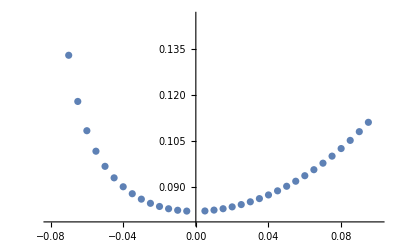

```mathematica
ListPlot[{{-0.005,0.0821359760983087},{-0.01,0.08240580649161566},{-0.015,0.08289601227467147},{-0.02,0.08363464105890822},{-0.025,0.08465888479752443},{-0.03,0.0860186658219999},{-0.035,0.08778218980513774},{-0.04,0.09004489576310176},{-0.045,0.09294460860131312},{-0.05,0.09668883245316781},{-0.055,0.10160804606863544},{-0.06,0.10827191890653429},{-0.065,0.11778744936280458},{-0.07,0.13280313774488595},{-0.075,0.1638795391281989},{-0.08,0.19999999999999982},{0.005,0.08217735929995362},{0.01,0.08246014362261234},{0.015,0.08290446036910926},{0.02,0.08350370995936329},{0.025,0.08425336015914237},{0.03,0.08515060748945469},{0.035,0.08619411847936137},{0.04,0.08738382890724322},{0.045,0.08872078530182631},{0.05,0.09020701711699664},{0.055,0.09184543083935509},{0.06,0.09363971927441178},{0.065,0.09559428066811626},{0.07,0.09771414335825496},{0.075,0.1000048924394375},{0.08,0.10247259557218752},{0.085,0.10512372563823658},{0.09,0.10796507849530634},{0.095,0.1110036846533724},{0.1,0.8960047446438754}}]
```

```mathematica
Manipulate[Plot[NullsHolm[Jtwo,z],{z,-1,1}],{Jtwo,-0.1,0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.79778}. NIntegrate obtained -0.48017 and 0.59425 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {1.85914}. NIntegrate obtained -0.0940284 and 0.310521 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.47886}. NIntegrate obtained 0.030441 and 0.0623251 for the integral and error estimates.

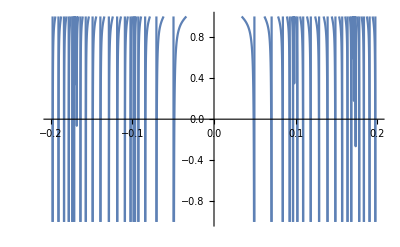

```mathematica
Plot[NullsHolm[-0.7,z],{z,-0.2,0.2},PlotRange->{-1,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {2.47886}. NIntegrate obtained 0.000482123 and 0.0509795 for the integral and error estimates.

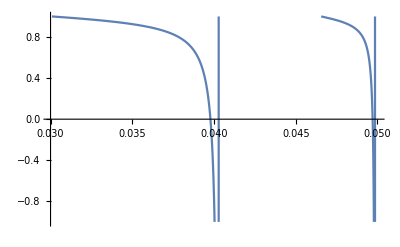

```mathematica
Plot[NullsHolm[-0.8,z],{z,0.03,0.05},PlotRange->{-1,1}]
```